## Analytical Mixing Model, v1 (50-50 mixes only) Last updated: February 5, 2019

```mathematica
ClearAll["Global`*"]
```

```mathematica
P1A[s1_,θ1A_,η_]:=s1^η/(s1^η+θ1A^η)
P2A[s2_,θ2A_,η_]:=s2^η/(s2^η+θ2A^η)
P1B[s1_,θ1B_,η_]:=s1^η/(s1^η+θ1B^η)
P2B[s2_,θ2B_,η_]:=s2^η/(s2^η+θ2B^η)
```

```mathematica
f1:=δ1 -(α1A*x1A + α1B*x1B)/n
f2:=δ2 -(α2A*x2A + α2B*x2B)/n
f3:=1/2*P1A[s1,θ1A,η](n/2-(x1A+x2A)) - τ*x1A
f4:=1/2*P2A[s2,θ2A,η](n/2-(x1A+x2A)) - τ*x2A
f5:=1/2*P1B[s1,θ1B,η](n/2-(x1B+x2B)) - τ*x1B
f6:=1/2*P2B[s2,θ2B,η](n/2-(x1B+x2B)) - τ*x2B

f3p:=1/2*P1A[s1,θ1A,η]*(2-P2A[s2,θ1A,η])*(n/2-(x1A+x2A)) - τ*x1A
f4p:=1/2*P2A[s2,θ1A,η]*(2-P1A[s1,θ1A,η])*(n/2-(x1A+x2A)) - τ*x2A
f5p:=1/2*P1B[s1,θ1A,η]*(2-P2B[s2,θ1A,η])*(n/2-(x1B+x2B)) - τ*x1B
f6p:=1/2*P2B[s2,θ1A,η]*(2-P1B[s1,θ1A,η])*(n/2-(x1B+x2B)) - τ*x2B
```

```mathematica
f1p:=f1/.x1B->0
f2p:=f2/.x2B->0
```

```mathematica
Solve[ f1==0 && f2==0 &&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,x1A,x2A,x1B,x2B}]
(*Takes too long*)
```

$Aborted

```mathematica
η=1;τ=0.2;
(*θ1A=10;θ2A=10;θ1B=10;θ2B=10;*)
θ1A=k;θ2A=k;θ1B=k;θ2B=k;
$Assumptions={s1,s2,x1A,x2A,x1B,x2B,δ1,δ2,α1A,α1B,α2A,α2B,θ1A,θ2A,θ1B,θ2B}∈Reals&&{s1,s2,x1A,x2A,x1B,x2B,δ1,δ2,α1A,α1B,α2A,α2B,θ1A,θ2A,θ1B,θ2B}≥0;
```

```mathematica
Off[Solve::ratnz];
(η=#;
eq=FullSimplify[Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,x1A,x2A,x1B,x2B}],$Assumptions];
(*eq2 = FullSimplify[Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,x1A,x2A,x1B,x2B}],$Assumptions];*)
eq2 = Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,x1A,x2A,x1B,x2B}];

Print[{"η = "<>ToString[#],Length@eq,DeleteDuplicates[{x1A,x2A,x1B,x2B}/.eq],Length@eq2,DeleteDuplicates[{x1A,x2A,x1B,x2B}/.eq2]}];&)/@ {1}(*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}*)
```

{η = 1,1,{{(n δ1)/(α1A+α1B),(n δ2)/(α2A+α2B),(n δ1)/(α1A+α1B),(n δ2)/(α2A+α2B)}},2,{{(n δ1)/(α1A+α1B),(n δ2)/(α2A+α2B),(n δ1)/(α1A+α1B),(n δ2)/(α2A+α2B)}}}

{Null}

```mathematica
Clear[δ1,δ2,α1A,α1B,α2A,α2B,n,θ1A,θ2A,θ1B,θ2B];
n=16.;(*θ1A=10.;θ2A=20.;θ1B=20.;θ2B=10.;*)
δ1=0.6; δ2=0.6;
(*Reduce[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0&&$Assumptions,{s1,s2,x1A,x2A,x1B,x2B}]*)
(*Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,x1A,x2A,x1B,x2B}]*)
θ1A =10 ; θ2A = 2*θ1A; θ1B = 2*θ1A; θ2B =θ1A;
α1A=2;α1B=α1A;α2A=α1A;α2B=α1A;

eq3=FullSimplify[Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,x1A,x2A,x1B,x2B}] ,$Assumptions];
eq4=DeleteDuplicates[FullSimplify[{x1A,x2A,x1B,x2B}/.eq3,$Assumptions]]
Length@eq4

f1
f2
f3
f4
f5
f6
```

{{25.8263,-21.0263,-21.0263,25.8263},{15.4212,-1.72162,-10.6212,6.52162},{6.52162,-10.6212,-1.72162,15.4212},{2.97371,1.82629,1.82629,2.97371}}

4

0.6-0.0625 (2 x1A+2 x1B)

0.6-0.0625 (2 x2A+2 x2B)

-0.2 x1A+(s1 (8.-x1A-x2A))/(2 (10+s1))

(s2 (8.-x1A-x2A))/(2 (20+s2))-0.2 x2A

-0.2 x1B+(s1 (8.-x1B-x2B))/(2 (20+s1))

(s2 (8.-x1B-x2B))/(2 (10+s2))-0.2 x2B

Why can’t the equilibria be computed when θ1B = θ2B = 2*θ1A???

```mathematica
FullSimplify[{f1,f2,f3,f4,f5,f6}/.{x1A->(n δ1)/(α1A+α1B),x2A->(n δ2)/(α2A+α2B),x1B->(n δ1)/(α1A+α1B),x2B->(n δ2)/(α2A+α2B)} ] // MatrixForm
```

(0
0
-(0.2 n δ1)/(α1A+α1B)+(n s1 (1-(2 δ1)/(α1A+α1B)-(2 δ2)/(α2A+α2B)))/(4 (k+s1))
-(0.2 n δ2)/(α2A+α2B)+(n s2 (1-(2 δ1)/(α1A+α1B)-(2 δ2)/(α2A+α2B)))/(4 (k+s2))
-(0.2 n δ1)/(α1A+α1B)+(n s1 (1-(2 δ1)/(α1A+α1B)-(2 δ2)/(α2A+α2B)))/(4 (k+s1))
-(0.2 n δ2)/(α2A+α2B)+(n s2 (1-(2 δ1)/(α1A+α1B)-(2 δ2)/(α2A+α2B)))/(4 (k+s2)))

```mathematica
eq2
```

{{s1→(0.5 (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2-1. √(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2),s2→(-2. k α2A δ1-2. k α2B δ1+2. k α1A δ2+2. k α1B δ2+(2.5 α1A α2A (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2-1. √(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(2.5 α1B α2A (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2-1. √(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(2.5 α1A α2B (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2-1. √(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(2.5 α1B α2B (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2-1. √(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)-(6. α2A δ1 (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2-1. √(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)-(6. α2B δ1 (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2-1. √(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)-(6. α1A δ2 (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2-1. √(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)-(6. α1B δ2 (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2-1. √(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2))/(5. α1A α2A+5. α1B α2A+5. α1A α2B+5. α1B α2B-12. α2A δ1-12. α2B δ1-12. α1A δ2-12. α1B δ2),x1A→(n δ1)/(α1A+α1B),x2A→(n δ2)/(α2A+α2B),x1B→(n δ1)/(α1A+α1B),x2B→(n δ2)/(α2A+α2B)},{s1→(0.5 (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2+√(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2),s2→(-2. k α2A δ1-2. k α2B δ1+2. k α1A δ2+2. k α1B δ2+(2.5 α1A α2A (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2+√(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(2.5 α1B α2A (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2+√(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(2.5 α1A α2B (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2+√(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(2.5 α1B α2B (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2+√(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)-(6. α2A δ1 (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2+√(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)-(6. α2B δ1 (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2+√(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)-(6. α1A δ2 (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2+√(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)-(6. α1B δ2 (10. k α1A α2A+10. k α1B α2A+10. k α1A α2B+10. k α1B α2B-26. k α2A δ1-26. k α2B δ1-22. k α1A δ2-22. k α1B δ2+√(-4. (4. k^2 α2A δ1+4. k^2 α2B δ1) (-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2)+(-10. k α1A α2A-10. k α1B α2A-10. k α1A α2B-10. k α1B α2B+26. k α2A δ1+26. k α2B δ1+22. k α1A δ2+22. k α1B δ2)^2)))/(-5. α1A α2A-5. α1B α2A-5. α1A α2B-5. α1B α2B+12. α2A δ1+12. α2B δ1+12. α1A δ2+12. α1B δ2))/(5. α1A α2A+5. α1B α2A+5. α1A α2B+5. α1B α2B-12. α2A δ1-12. α2B δ1-12. α1A δ2-12. α1B δ2),x1A→(n δ1)/(α1A+α1B),x2A→(n δ2)/(α2A+α2B),x1B→(n δ1)/(α1A+α1B),x2B→(n δ2)/(α2A+α2B)}}

## Analytical Mixing Model, v2 (mixes with different fractions of A individuals) Last updated: February 9, 2019

```mathematica
ClearAll["Global`*"]
```

```mathematica
P1A[s1_,θ1A_,η_]:=s1^η/(s1^η+θ1A^η)
P2A[s2_,θ2A_,η_]:=s2^η/(s2^η+θ2A^η)
P1B[s1_,θ1B_,η_]:=s1^η/(s1^η+θ1B^η)
P2B[s2_,θ2B_,η_]:=s2^η/(s2^η+θ2B^η)
```

```mathematica
f1:=δ1 -(α1A*x1A + α1B*x1B)/n
f2:=δ2 -(α2A*x2A + α2B*x2B)/n
f3:=1/2*P1A[s1,θ1A,η](f*n-(x1A+x2A)) - τ*x1A
f4:=1/2*P2A[s2,θ2A,η](f*n-(x1A+x2A)) - τ*x2A
f5:=1/2*P1B[s1,θ1B,η]((1.-f)*n-(x1B+x2B)) - τ*x1B
f6:=1/2*P2B[s2,θ2B,η]((1.-f)*n-(x1B+x2B)) - τ*x2B

f3p:=1/2*P1A[s1,θ1A,η]*(2-P2A[s2,θ1A,η])*(f*n-(x1A+x2A)) - τ*x1A
f4p:=1/2*P2A[s2,θ1A,η]*(2-P1A[s1,θ1A,η])*(f*n-(x1A+x2A)) - τ*x2A
f5p:=1/2*P1B[s1,θ1A,η]*(2-P2B[s2,θ1A,η])*((1.-f)*n-(x1B+x2B)) - τ*x1B
f6p:=1/2*P2B[s2,θ1A,η]*(2-P1B[s1,θ1A,η])*((1.-f)*n-(x1B+x2B)) - τ*x2B
```

```mathematica
f1p:=f1/.x1B->0
f2p:=f2/.x2B->0
```

```mathematica
(*Solve[ f1==0 && f2==0 &&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,x1A,x2A,x1B,x2B}]
(*Takes too long*)*)
```

```mathematica
(*τ=1;*)
(*θ1A=10;θ2A=10;θ1B=10;θ2B=10;*)
θ1A=k;θ2A=k;θ1B=k;θ2B=k;
$Assumptions={s1,s2,x1A,x2A,x1B,x2B,δ1,δ2,α1A,α1B,α2A,α2B,θ1A,θ2A,θ1B,θ2B,f}∈Reals&&{s1,s2,x1A,x2A,x1B,x2B,δ1,δ2,α1A,α1B,α2A,α2B,θ1A,θ2A,θ1B,θ2B,f}≥0 && f≤1;
```

```mathematica
Off[Solve::ratnz];
(η=#;
eq=FullSimplify[Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,x1A,x2A,x1B,x2B}],$Assumptions];
(*eq2 = FullSimplify[Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,x1A,x2A,x1B,x2B}],$Assumptions];*)
eq2 = Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,x1A,x2A,x1B,x2B}];

Print[{"η = "<>ToString[#],Length@eq,FullSimplify@DeleteDuplicates[{x1A,x2A,x1B,x2B}/.eq],Length@eq2,FullSimplify@DeleteDuplicates[{x1A,x2A,x1B,x2B}/.eq2]}];&)/@ {1,2,3,4,5,6,7}(*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}*)
```

{η = 1,1,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},2,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 2,4,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},8,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 3,9,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},18,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 4,16,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},32,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 5,25,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},50,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 6,36,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},72,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{η = 7,49,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}},98,{{(f n δ1)/(f α1A+α1B-1. f α1B),(f n δ2)/(f α2A+α2B-1. f α2B),((1.-1. f) n δ1)/(f α1A+α1B-1. f α1B),((1.-1. f) n δ2)/(f α2A+α2B-1. f α2B)}}}

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
η=3; δ1=0.6; δ2 = δ1 ; k = 10; τ=0.2; f = 0.5; n = 16;b =1;
α1A = 2; α2A = 2; α1B =b; α2B =b;
eqeq = FullSimplify[Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,x1A,x2A,x1B,x2B}],$Assumptions];
{s1,s2,x1A,x2A,x1B,x2B, (x1A+x2A+x1B+x2B)/n ,(x1A+x2A+x1B+x2B)/n≤ 1}/.eqeq// MatrixForm

DeleteDuplicates[f1/.eqeq]
DeleteDuplicates[f2/.eqeq]
```

(-14.7913 | -14.7913 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-14.7913 | 7.39564-12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-14.7913 | 7.39564+12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366-9.29419 ⅈ | -5.366-9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366-9.29419 ⅈ | -5.366+9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366-9.29419 ⅈ | 10.732 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366+9.29419 ⅈ | -5.366-9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366+9.29419 ⅈ | -5.366+9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
-5.366+9.29419 ⅈ | 10.732 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564-12.8096 ⅈ | -14.7913 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564-12.8096 ⅈ | 7.39564-12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564-12.8096 ⅈ | 7.39564+12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564+12.8096 ⅈ | -14.7913 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564+12.8096 ⅈ | 7.39564-12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
7.39564+12.8096 ⅈ | 7.39564+12.8096 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
10.732 | -5.366-9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
10.732 | -5.366+9.29419 ⅈ | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True
10.732 | 10.732 | 3.2 | 3.2 | 3.2 | 3.2 | 0.8 | True)

{-1.11022×10^-16}

{-1.11022×10^-16}

OK, let’s plot these and see if we can get something similar to Chris’s results!

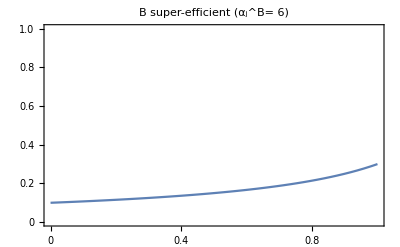

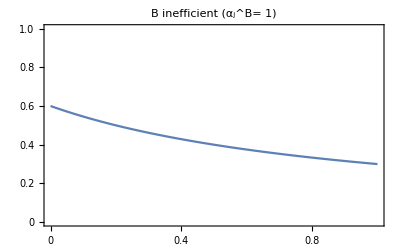

```mathematica
a1 = 2;
a2 = 6;
Plot[0.6/(f*a1+(1-f)*a2),{f,0,1},PlotRange->{{0,1},{0,1}},PlotLabel->"B super-efficient (α_j^B= 6)",
Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{None,"Frac. of colony on task j"},{None,"Frac. of A individuals (f)"}},FrameTicks->All]

a2 = 1;
Plot[0.6/(f*a1+(1-f)*a2),{f,0,1},PlotRange->{{0,1},{0,1}},PlotLabel->"B inefficient (α_j^B= 1)",
Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{None,"Frac. of colony on task j"},{None,"Frac. of A individuals (f)"}},FrameTicks->All]
```